# 1. izpit – Mathematica

## Računalniški praktikum 2023/24

Študijske smeri: Finančna matematika

## Podatki o študentu

Vpišite svoje podatke

Ime:

Priimek:

Vpisna številka:

## Navodila

Čas reševanja za celoten izpit je 120 minut.
V tem delu izpita so tri naloge, ki so skupaj vredne 30 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.
Dovoljeno je uporabljati dokumentacijo o Mathematici in gradivo iz vaj.
Vsakršna komunikacija je prepovedana.

## 1. naloga [10 točk]

1. (5 točk) Izračunajte vrsto .
 2. (5 točk) Izračunajte integral

```mathematica
Sum[1/n^2,{n,1,∞}]
```

π^2/6

```mathematica
Integrate[Sqrt[x/(1-x)],{x,0,1}]
```

π/2

## 2. naloga [10 točk]

1. (5 točk) Definirajte funkcijo  f, ki sprejme parametra x in y in ima predpis .
2. (5 točk) Narišite graf implicitno podane funkcije, ko je   za  in  .

```mathematica
f[x_,y_]:=(x^2+y^2)^2-y^2-x*(x^2+y^2)
```

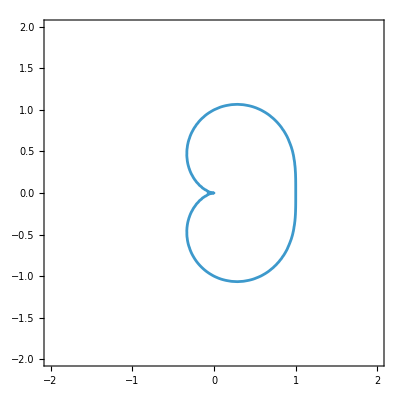

```mathematica
ContourPlot[f[x,y]==0,{x,-2,2},{y,-2,2}]
```

## 3. naloga [10 točk]

1. (4 točke) V spremenljivko potence shranite vse lihe potence števila 2 od 1 do 25, od katerih odštejete 1: 1, 7, 31, 127 ... Pomagajte si z ukazom Table.
2. (4 točke) Izberite vsa števila iz seznama potenc, ki so praštevila. 
3. (2 točki) Naredite enako še za sode potence.

```mathematica
Table[2^n-1,{n,1,25,2}]
```

{1,7,31,127,511,2047,8191,32767,131071,524287,2097151,8388607,33554431}

```mathematica
Table[Select{1,7,31,127,511,2047,8191,32767,131071,524287,2097151,8388607,33554431},PrimeQ]
```

Table::nliter: Nonlist iterator PrimeQ at position 2 does not evaluate to a real numeric value.

Table[Select {1,7,31,127,511,2047,8191,32767,131071,524287,2097151,8388607,33554431},PrimeQ]

```mathematica
Select[{1,7,31,127,511,2047,8191,32767,131071,524287,2097151,8388607,33554431},PrimeQ]
```

{7,31,127,8191,131071,524287}

Reduce::naqs: 1&&7&&31&&127&&511&&2047&&8191&&32767&&131071&&524287&&2097151&&8388607&&33554431 is not a quantified system of equations and inequalities.

Reduce[{1,7,31,127,511,2047,8191,32767,131071,524287,2097151,8388607,33554431},Primes]

-1+2^n∈Primes

Table::nliter: Nonlist iterator Primes at position 3 does not evaluate to a real numeric value.

Table[2^n-1,{n,1,25,2},Primes]

```mathematica
Table[2^n-1,{n,0,25,2}]
```

{0,3,15,63,255,1023,4095,16383,65535,262143,1048575,4194303,16777215}

```mathematica
Select[{0,3,15,63,255,1023,4095,16383,65535,262143,1048575,4194303,16777215},PrimeQ]
```

{3}